```mathematica
name[28]="Y";
name[29]="LS";
name[1]="SS";
name[2]="FH";
name[3]="4K9";
name[4]="4K13";
name[5]="4K14";
name[6]="4K17";
name[7]="4K18";
name[n_]:="3K"<>ToString[n];
name[30]="";
```

```mathematica
poss[28]=Table[{n,n,n,n,n},{n,1,6}];
poss[29]=Permutations[Range[5]]~Join~Permutations[Range[2,6]];
poss[1]=Complement[Flatten[Table[Permutations[{n,n+1,n+2,n+3,m}],{n,1,3},{m,1,6}],2],poss[29]];poss[2]=Complement[Flatten[Table[Permutations[{n,n,n,m,m}],{n,1,6},{m,1,6}],2],poss[28]];
kind4=Complement[Flatten[Table[Permutations[{n,n,n,n,m}],{n,1,6},{m,1,6}],2],poss[28]];
poss[3]=Select[kind4,Total[#]==9&];
poss[4]=Select[kind4,Total[#]==13&];
poss[5]=Select[kind4,Total[#]==14&];
poss[6]=Select[kind4,Total[#]==17&];
poss[7]=Select[kind4,Total[#]==18&];
kind3=Complement[Flatten[Table[Permutations[{n,n,n,m,p}],{n,1,6},{m,1,6},{p,1,6}],3],poss[28],poss[2],kind4];
poss[n_]:=Select[kind3,Total[#]==n&];
poss[30]:=Flatten[Table[{i,j,k,n,m},{i,1,6},{j,1,6},{k,1,6},{n,1,6},{m,1,6}],4];
```

```mathematica
r:=Module[{},
s=RandomInteger[{1,6}];
If[s<3,Return[s]];
If[s==4,Return[s+25]];
If[s==5,Return[RandomInteger[{3,7}]]];
If[s==6,RandomInteger[{8,27}],30]]
```

```mathematica
rowlen[n_]:=Length[poss[rowspectrum[[n]]]]
```

```mathematica
collen[n_]:=Length[poss[colspectrum[[n]]]]
```

```mathematica
check[L_]:=Apply[And,Table[MemberQ[poss[rowspectrum[[n]]],L[[n]]],{n,1,5}]]&&Apply[And,Table[MemberQ[poss[colspectrum[[n]]],Transpose[L][[n]]],{n,1,5}]]
```

```mathematica
initialize:=Module[{},
colspectrum={r,r,r,r,r};rowspectrum={r,r,r,r,r};
While[Apply[Times,Map[rowlen,Range[5]]]>10^15||Apply[Times,Map[collen,Range[5]]]>10^15||(MemberQ[rowspectrum,28]&&MemberQ[colspectrum,28])||(MemberQ[rowspectrum,30]&&MemberQ[colspectrum,30])||(Length[Union[Select[rowspectrum,#<30&]]]<Length[Select[rowspectrum,#<30&]])||(Length[Union[Select[colspectrum,#<30&]]]<Length[Select[colspectrum,#<30&]]),colspectrum={r,r,r,r,r};rowspectrum={r,r,r,r,r}]]
```

```mathematica
agrees[q1_,q2_]:=Total[Abs[q1-q2]*q2]==0
```

```mathematica
beforepic:=Style[Graphics[{
Table[Line[{{0,i},{5,i}}],{i,0,5}],
Table[Line[{{i,0},{i,5}}],{i,0,5}],
MapIndexed[Text[name[#1],{5.5,#2[[1]]-1/2}]&,colspectrum],
MapIndexed[Text[name[#1],{#2[[1]]-1/2,-.5}]&,rowspectrum]
},ImageSize->180],Antialiasing->False]
```

```mathematica
d[{x_,y_}]:=Disk[{x-1/2,y-1/2},.1]
```

```mathematica
afterpic[s_]:=Graphics[{
Style[{Table[Line[{{0,i},{5,i}}],{i,0,5}],
Table[Line[{{i,0},{i,5}}],{i,0,5}]},Antialiasing->False],
MapIndexed[Text[name[#1],{5.5,#2[[1]]-1/2}]&,colspectrum],
MapIndexed[Text[name[#1],{#2[[1]]-1/2,-.5}]&,rowspectrum],
MapIndexed[Which[#1==1,d[#2],#1==2,{d[#2+.3],d[#2-.3]},#1==3,{d[#2+.3],d[#2-.3],d[#2]},#1==4,{d[#2+.3],d[#2-.3],d[#2-{.3,-.3}],d[#2+{.3,-.3}]},#1==5,{d[#2+.3],d[#2-.3],d[#2-{.3,-.3}],d[#2+{.3,-.3}],d[#2]},#1==6,{d[#2+.3],d[#2-.3],d[#2-{.3,-.3}],d[#2+{.3,-.3}],d[#2+{.3,0}],d[#2-{.3,0}]}]&,s,{2}]
},ImageSize->180]
```

```mathematica
findsolns:=Module[{},
initialize;(*Print[Map[name,rowspectrum],Map[name,colspectrum]];*)
stac={Table[0,{i,5},{j,5}]};
solns={};
While[Length[stac]>0&&Length[solns]≤2,
cur=First[stac];
stac=Rest[stac];
zeroes=Position[cur,0];
If[zeroes=={},If[check[cur],AppendTo[solns,cur]],
zt=Transpose[zeroes];
zrow=Map[rowlen,Union[zt[[1]]]];
zcol=Map[collen,Union[zt[[2]]]];
zmin=Min[zrow~Join~zcol];
If[MemberQ[zrow,zmin],
row=Select[Union[zt[[1]]],rowlen[#]==zmin&][[1]];
possrow=Select[poss[rowspectrum[[row]]],agrees[#,cur[[row]]]&];
stac=Map[ReplacePart[cur,row->#]&,possrow]~Join~stac
,
col=Select[Union[zt[[2]]],collen[#]==zmin&][[1]];
posscol=Select[poss[colspectrum[[col]]],agrees[#,Transpose[cur][[col]]]&];
stac=Map[Transpose[ReplacePart[Transpose[cur],col->#]]&,posscol]~Join~stac]]]]
```

```mathematica
Map[Length[poss[#]]&,Range[30]]
```

{960,300,10,10,10,10,10,20,20,60,60,80,60,60,100,80,60,60,80,100,60,60,80,60,60,20,20,6,240,7776}

1 solutions

7.73967×10^6

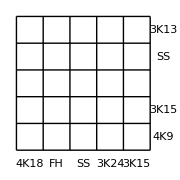

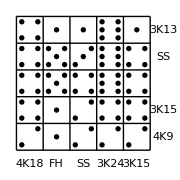

1 solutions

6.60452×10^6

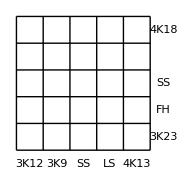

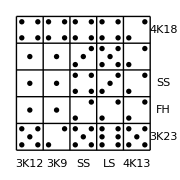

1 solutions

8062.16

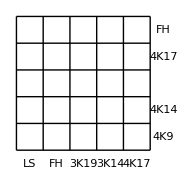

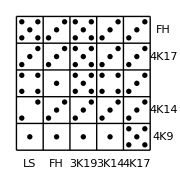

1 solutions

1.39314×10^7

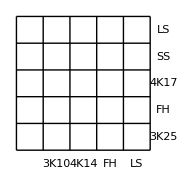

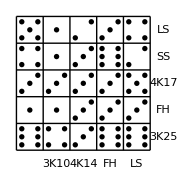

1 solutions

206391.

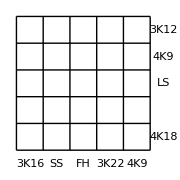

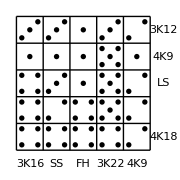

1 solutions

74649.6

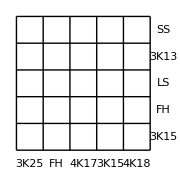

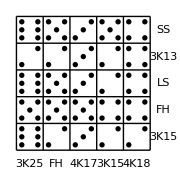

1 solutions

154793.

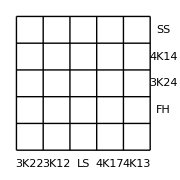

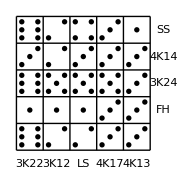

1 solutions

134369.

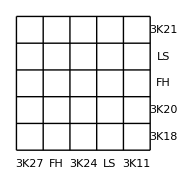

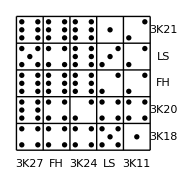

```mathematica
For[w=1,w>0,w++,
findsolns;
If[Length[solns]==1,
Print[Length[solns]," solutions"];
Print[N[Apply[Times,Map[rowlen,Range[5]]~Join~Map[collen,Range[5]]]/10^15]];
Print[beforepic];
Print[Map[afterpic,solns]]]]
```